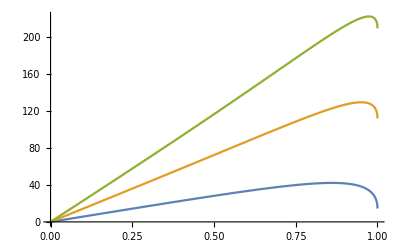

```mathematica
n=1.333;
α[x_]:=ArcSin[x];
β[x_,n_]:=ArcSin[x/n];
ρ[x_,n_,c_]:=-2α[x]/Degree+(2+2c)β[x,n]/Degree;
ρ1[x_,n_]:=-2α[x]/Degree+4β[x,n]/Degree;
ρ2[x_,n_]:=-2α[x]/Degree+6β[x,n]/Degree;
ρ3[x_,n_]:=-2α[x]/Degree+8β[x,n]/Degree;
Plot[{ρ[x,n,1],ρ[x,n,2],ρ[x,n,3]},{x,0,1}]
```

```mathematica
N[1/Degree]
```

57.2958

```mathematica
Solve[D[ρ[x,nn,cc],x]==0,x]
```

{{x→-(√(1+2 cc+cc^2-nn^2))/(√cc √(2+cc))},{x→(√(1+2 cc+cc^2-nn^2))/(√cc √(2+cc))}}

```mathematica
Solve[D[ρ3[x,y],x]==0,x]
```

{{x→-(√(16-y^2))/(√15)},{x→(√(16-y^2))/(√15)}}

```mathematica
{{Derivative[1,0][ρ1][x,y]->0}}
```

{{ρ1^(1,0)[x,y]→0}}

```mathematica
D[ρ1[x,y],x]
```

-2/(° √(1-x^2))+4/(° √(1-x^2/y^2) y)

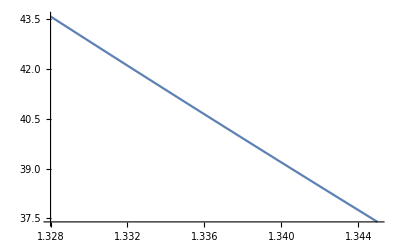

```mathematica
Plot[ρ3[(√(16-y^2))/(√15),y],{y,1.328,1.345}]
```

```mathematica
ρ2[(√(16-1.334^2))/(√15),1.344]
ρ2[(√(16-1.332^2))/(√15),1.332]
```

-55.1034

-51.8549

```mathematica
n=1.31;
ksi=ArcSin[1/n];
lambda=Pi/2-ksi;
h =90- ArcSin[n*Sin[lambda]]/Degree
```

32.1964

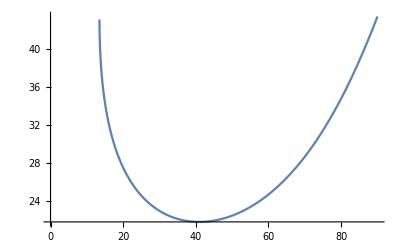

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→ConditionalExpression[40.9196+360. C[1], C[1]∈ℤ]}}

```mathematica
n=1.31;
bb[a_,n_]:=ArcSin[Sin[a]/n];
aa[b_,n_]:=ArcSin[n*Sin[Pi/3-b]];
halo22[i_,n_]:=i -Pi/3+aa[bb[i ,n],n]
Plot[halo22[x*Degree,n]/Degree ,{x,0,90}]
res=Solve[D[halo22[x*Degree,n],x]==0,x, Reals]
```

```mathematica
Reduce[res[[1]][[1]][[2]]]
```

Reduce::naqs: 1∈&&40.9196+360. 1 is not a quantified system of equations and inequalities.

Reduce[ConditionalExpression[40.9196+360. C[1], C[1]∈ℤ]]

```mathematica
ConditionalExpression[40.9196499548851+360. C[1], C[1]∈Integers]
```